```mathematica
SetDirectory[NotebookDirectory[]]
```

/Users/lukastk/dev/lukas-phdwork/thesis/figs/cosserat_surface

```mathematica
xmin=-3;
xmax = 3;
ymin=-2;
ymax=2;

Nx = 5;
Ny =5;

directorThickness = 0.015;
directorArrowHeadSize = 0.02;
directorColor=RGBColor[0.17,0.32,1];
director2Color=RGBColor[0.17,0.32,1,0.2];
```

```mathematica
surface1[x_,y_]:=Sin[x+y];
surface2[x_,y_]:=1.2Cos[x+y]+0.8Sin[x+y]+3;
surface3[x_,y_]:=surface1[x,y]-(surface2[x,y]-surface1[x,y]);
surface1Plot = Plot3D[surface1[x,y],{x,xmin,xmax},{y,ymin,ymax},
PlotStyle->Gray,
Axes->False,Mesh->Full,Boxed->False,PlotRange->All,
AspectRatio->1];
surface2Plot = Plot3D[surface2[x,y],{x,xmin,xmax},{y,ymin,ymax},
PlotStyle->RGBColor[0.85,0.32,0.29,0.5],
Axes->False,Mesh->None,Boxed->False,PlotRange->All];
surface3Plot = Plot3D[surface3[x,y],{x,xmin,xmax},{y,ymin,ymax},
PlotStyle->RGBColor[0.85,0.32,0.29,0.1],
Axes->False,Mesh->None,Boxed->False,PlotRange->All];
```

```mathematica
directordx[x_,y_]:=Sin[2 Pi(x-xmin)/(xmax-xmin)] Sin[2 Pi(y-ymin)/(ymax-ymin)]/5
directordy[x_,y_]:=Sin[2 Pi(x-xmin)/(xmax-xmin)] Sin[2 Pi(y-ymin)/(ymax-ymin)]/5
```

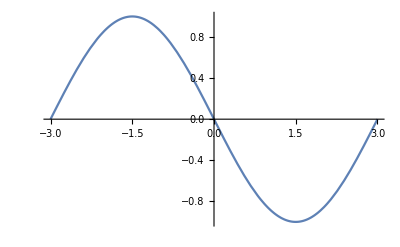

```mathematica
Plot[Sin[2 Pi(x-xmin)/(xmax-xmin)],{x,xmin,xmax}]
```

```mathematica
directorsBase = Flatten[
Table[
{x,y,surface1[x,y]}
,{x,Array[#&,Nx,{xmin,xmax}]}, {y,Array[#&,Ny,{ymin,ymax}]}]
,1];
directorsTip= Flatten[
Table[
{x+directordx[x,y],y+directordy[x,y],surface2[x+directordx[x,y],y+directordy[x,y]]}
,{x,Array[#&,Nx,{xmin,xmax}]}, {y,Array[#&,Ny,{ymin,ymax}]}]
,1];
directorsTip2= Table[
directorsBase[[i]]-(directorsTip[[i]]-directorsBase[[i]]),
{i, 1, Length[directorsBase]}];

directors = Table[
Arrow[Tube[{directorsBase[[i]], directorsTip[[i]]},directorThickness]]
,{i, 1, Length[directorsBase]}];
directors2 = Table[
Arrow[Tube[{directorsBase[[i]], directorsTip2[[i]]},directorThickness]]
,{i, 1, Length[directorsBase]}];
```

```mathematica
fig=Show[{
surface1Plot,
surface2Plot,
surface3Plot,
Graphics3D[{directorColor,Arrowheads[directorArrowHeadSize],Thickness[directorThickness], directors}],
Graphics3D[{director2Color,Arrowheads[directorArrowHeadSize],Thickness[directorThickness], directors2}]
},ImageSize->Large]
```

-Graphics3D-

```mathematica
(*Export["cosserat_surface.png",fig,ImageResolution-> 400,Background->None];*)
```